```mathematica
coef[k_]:=0.5∫_-1^1 t*ⅇ^(-I*Pi*t*k)ⅆt
```

```mathematica
func[x_]=∑_(k=-20)^20 coef[k]*ⅇ^(I Pi k x);
```

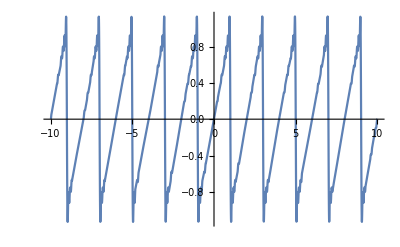

```mathematica
Plot[func[x],{x,-10,10}]
```